# Figure 4

All data were generated with julia code https://github.com/djuliannader/RabiModel.git

#### (a)

```mathematica
Datratio={{0.4,1.4010043181185432/(3*0.6842257819833207^2)},{0.715,2.0647788577794306/(3*0.8386441314345895^2)},{0.716,3.1910527741596697/(3*1.0807581600041647^2)},{0.7165,7.068549248089215/(3*1.8381566740804358^2)},{0.7167,12.540447165722908/(3*2.8040991976189904^2)},{0.7168,4.281019927997758/(3*0.8331672780526546^2)},{0.717,1.1560381510015576/(3*0.4126601010748559^2)},{0.72,1.0910956685142317/(3*0.6071421657007087^2)},{0.75,1.3492500474141749/(3*0.6714095041954184^2)},{1,1.340308751699645/(3*0.6691860193491785^2)},{1.3,1.1319757914233515/(3*0.615056513422879^2)},{1.35,0.9732694531632796/(3*0.570876923764255^2)},{1.39,0.6630503078209864/(3*0.47460641476785254^2)},{1.4,0.5203437591630683/(3*0.42355621883218825^2)},{1.41,0.34829800938262073/(3*0.34839059445427^2)},{1.42,0.33996343882151553/(3*0.2707937926473275^2)},{1.425,0.7796890426247968/(3*0.3248410060850596^2)},{1.43,5.113274633036904/(3*1.9087630356581253^2)},{1.435,3.176952834539897/(3*1.4102429537346952^2)},{1.44,2.9255481197342186/(3*1.1624342844485611^2)},{1.45,2.9255481197342186/(3*1.1624342844485611^2)},{1.46,9.386477831912876/(3*1.7939806141073507^2)},{1.47,4.918898234746633/(3*1.2204852511849429^2)},{1.48,3.202853387494719/(3*1.0216612478118434^2)},{1.49,2.6838382103032004/(3*0.9439992095178302^2)},{1.5,2.421434277964104/(3*0.898492341570884^2)},{1.55,1.928557166108979/(3*0.8032728100504959^2)},{1.75,1.612016996371311/(3*0.7341522236842887^2)},{2.85,1.510665718701256/(3*0.7061719159221853^2)},{2.89,2.4530029032379472/(3*0.7554803733168849^2)}
,{2.8918,7.529992378191963/(3*2.1055255981458543^2)},{2.9,1.4168283860417321/(3*0.707661709084062^2)},{3.0,1.480878063439686/(3*0.7053537529131758^2)},{3.2,1.4824563807095834/(3*0.7046323759013358^2)}};
```

```mathematica
Dataratio=Table[{(2π/(2*4.393835879146564))/Datratio[[i,1]],Datratio[[i,2]]},{i,1,Length[Datratio]}];
```

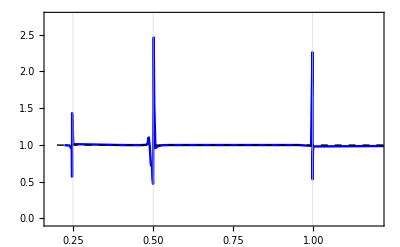

```mathematica
fig4a=Show[ListPlot[Dataratio,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.05,2.75}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.466448498970723/(3*0.7002235674837912^2),{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (b)

```mathematica
Datnn={{0.4,1*10^(-10)},{0.715,1.6*10^(-6)},{0.716,0.005590196863773933},{0.7165,0.12408411806264019},{0.7167,0.361350129435033},{0.7168,0.3505284194979199},{0.717,0.12199277461195868},{0.7175,0.007254653582490889},{0.72,1*10^(-12)},{1.0,5*10^(-9)},{1.39,7.4*10^(-7)},{1.40,0.0002148151597571868},{1.41,0.004389},{1.42,0.0616507676777347},{1.425,0.18302082837875622},{1.43,0.49546082594159047},{1.435,0.38274873130051246},{1.44,0.33789819637431735},{1.45,0.2669658864328162},{1.46,0.21485947757188084},{1.47,0.0538995259983881},{1.48,0.006226983441246503},{1.49,0.0006176444769232514},{1.5,0.0000016444769232514},{2.85,1.7*10^(-9)},{2.88,4.93*10^(-5)},{2.885,0.0006348265203179881},{2.889,0.011673325218100494},{2.89,0.03471265933763723},{2.891,0.16842500447752262},{2.8915,0.16842500447752262},{2.8918,0.5481166446620327},{2.892,0.4172747876468874},{2.893,0.06130663855310359},{2.895,0.00787467886520088},{2.9,0.00048104447680907825},{3.2,1.8*10^(-8)}};
```

```mathematica
Dataneg=Table[{(2π/(2*4.393835879146564))/Datnn[[i,1]],Datnn[[i,2]]},{i,1,Length[Datnn]}];
```

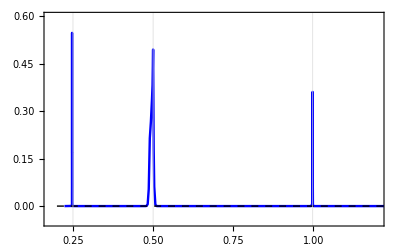

```mathematica
fig4b=Show[ListPlot[Dataneg,Joined->True,PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.05,0.6}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[00,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (c)

```mathematica
Datimp={{0.4,0.9941545393058486},{0.715,0.9928259803016749},{0.716,0.9907739324098565},{0.7165,0.9844189838590961},{0.7167,0.976428512810312},{0.7168,0.9931069568140486},{0.717,0.9965594057066974},{0.72,0.9934136182043649},{1,0.9942689896520094},{1.3,0.9947329114514543},{1.35,0.9951136336034596},{1.39,0.9959477155719239},{1.4,0.9963926573380568},{1.41,0.9970522456400086},{1.42,0.9977517493636212},{1.425,0.9973106880438388},{1.43,0.9835704874471598},{1.435,0.98781084854633},{1.44,0.9899983441080579},{1.45,0.9850385481702049},{1.46,0.989692106847473},{1.47,0.989692106847473},{1.48,0.9912977892879522},{1.49,0.9919405918632429},{1.5,0.992321459236589},{1.51,0.9925815314323458},{1.52,0.9927713156223413},{2.8,0.9939506946093359},{2.85,0.9939533851274481},{2.88,0.9939512254815185},{2.885,0.9939387654865846},{2.889,0.9938242922838461},{2.89,0.9936081490783562},{2.891,0.9920103948842475},{2.8918,0.9820755487784025},{2.892,0.9870634714740187},{2.893,0.9932682531174318},{2.895,0.9938308317049},{2.9,0.993929961881876},{3.2,0.9939645620618205}};
```

```mathematica
Dataimp=Table[{(2π/(2*4.393835879146564))/Datimp[[i,1]],1-Datimp[[i,2]]},{i,1,Length[Datimp]}];
```

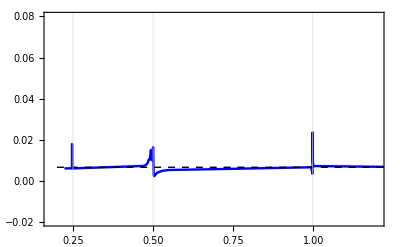

```mathematica
fig4c=Show[ListPlot[Dataimp,Joined->True,PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.02,0.08}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1-0.9934136182043661,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (d)

```mathematica
Datfis={{0.4,1.8188541861330119},{0.7,1.8388028322816627},{0.71,1.874127143527024},{0.715,1.964603626943625},{0.7155,1.9804073771782498},{0.716,1.9723442303712588},{0.7165,1.6912235590856355},{0.7167,1.1296157254529111},{0.72,1.5501509199699097},{0.725,1.7407462741455948},{0.73,1.766165130060758},{0.75,1.791533329557357},{0.8,1.798893350090337},{0.85,1.7982959049747447},{0.9,1.7957331350439623},{0.95,1.7919587361168188},{1,1.7862909410235246},{1.05,1.7790476173058452},{1.1,1.7689731046925083},{1.15,1.7543659541691137},{1.2,1.7315651395102485},{1.25,1.691319570040237},{1.28,1.6481618171081696},{1.3,1.6018938544201682},{1.32,1.5262648148342361},{1.34,1.3826899818995384},{1.36,1.0338825965291356},{1.38,0.1459688570586324},{1.4,1.6701910152864137},{1.42,1.7890158168263173},{1.44,2.83178092329614},{1.46,3.3271493779904766},{1.48,2.279060956596594},{1.5,2.0845623441769057},{1.55,1.9783566816018272},{1.7,1.908080803068404},{2,1.8761201442897903},{2.2,1.868687381585609},{2.4,1.8648706771509123},{2.6,1.8638288701223988},{2.8,1.8729629122043518},{2.85,1.428141538712384},{2.88,2.0336990375701696},{2.9,1.8184114092972472},{2.95,1.8345642774190547},{3,1.8433194470750665},{3.2,1.8497583055711244}};
```

```mathematica
Datafisher=Table[{(2π/(2*4.393835879146564))/Datfis[[i,1]],Datfis[[i,2]]},{i,1,Length[Datfis]}];
```

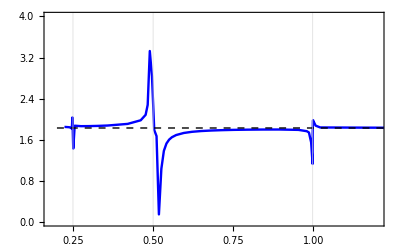

```mathematica
fig4d=Show[ListPlot[Datafisher,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{0,4}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.8283437968627987,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (e)

```mathematica
DatexpH0={{0.4,-25.141783302042157},{0.715,-25.135858983595167},{0.716,-25.10524395557744},{0.7165,-24.919655492938094},{0.7167,-24.5494225580958},{0.7168,-24.566209304699377},{0.717,-24.916742120658352},{0.7175,-25.097286539660953},{0.72,-25.13822260636248},{1,-25.141535360681715},{1.3,-25.138903751436743},{1.35,-25.134427475285378},{1.39,-25.11434567072431},{1.4,-25.09500286593096},{1.41,-25.045414826323864},{1.42,-24.86505946921965},{1.425,-24.60185571064829},{1.43,-24.38035777402412},{1.435,-24.66457054842873},{1.44,-24.623331184264973},{1.45,-24.755882720527573},{1.46,-24.90060912510621},{1.47,-25.076648729465195},{1.48,-25.115280750395698},{1.49,-25.125500026842353},{1.5,-25.13047959935979},{1.55,-25.138434781241838},{2,-25.14177271554673},{2.88,-25.14132010914874},{2.885,-25.14018188749598},{2.89,-25.116080531048603},{2.891,-25.00574209788232},{2.8915,-24.43593684720496},{2.893,-25.099345958969057},{2.895,-25.134983064972815},{2.9,-25.140778981025072},{3.2,-25.14188070393656}};
Datnn={{0.4,1*10^(-10)},{0.715,1.6*10^(-6)},{0.716,0.005590196863773933},{0.7165,0.12408411806264019},{0.7167,0.361350129435033},{0.7168,0.3505284194979199},{0.717,0.12199277461195868},{0.7175,0.007254653582490889},{0.72,1*10^(-12)},{1.0,5*10^(-9)},{1.39,7.4*10^(-7)},{1.40,0.0002148151597571868},{1.41,0.004389},{1.42,0.0616507676777347},{1.425,0.18302082837875622},{1.43,0.49546082594159047},{1.435,0.38274873130051246},{1.44,0.33789819637431735},{1.45,0.2669658864328162},{1.46,0.21485947757188084},{1.47,0.0538995259983881},{1.48,0.006226983441246503},{1.49,0.0006176444769232514},{1.5,0.0000016444769232514},{2.85,1.7*10^(-9)},{2.88,4.93*10^(-5)},{2.885,0.0006348265203179881},{2.889,0.011673325218100494},{2.89,0.03471265933763723},{2.891,0.16842500447752262},{2.8915,0.16842500447752262},{2.8918,0.5481166446620327},{2.892,0.4172747876468874},{2.893,0.06130663855310359},{2.895,0.00787467886520088},{2.9,0.00048104447680907825},{3.2,1.8*10^(-8)}};
```

```mathematica
DataexpH0=Table[{(2π/(2*4.393835879146564))/DatexpH0[[i,1]],DatexpH0[[i,2]]/50},{i,1,Length[DatexpH0]}];
```

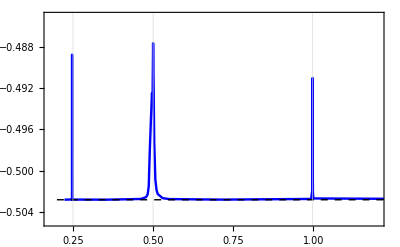

```mathematica
fig4e=Show[ListPlot[DataexpH0,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.505,-0.485}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[-25.142253953183587/50,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```